## Линейное

#### Симметричный

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Integtgro_interpolation_mult_0.500000.txt"]],Table[Real,n+1]];
(*k = plots⟦Length[plots]⟧⟦1⟧+1;
m = plots⟦Length[plots]⟧⟦2⟧+1;
TAll = {};
For[j=0,j<k,j++;
T = {};
For[i = 0,i <m,i++;
T = AppendTo[T,{plots⟦(j-1)*m +i⟧⟦2⟧,plots⟦(j-1)*m+i⟧⟦3⟧}]];
TAll = AppendTo[TAll,T]]*)
```

```mathematica
(*Manipulate[ListContourPlot[TAll⟦i⟧],{i,1,k-1}]*)
```

```mathematica
ListPlot3D[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

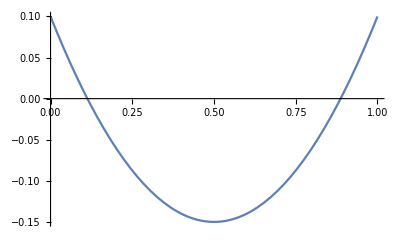

```mathematica
Plot[x^2-x+0.1,{x,0,1}]
```

#### Явный

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Integtgro_interpolation_mult_0.000000.txt"]],Table[Real,n+1]];
(*k = plots⟦Length[plots]⟧⟦1⟧+1;
m = plots⟦Length[plots]⟧⟦2⟧+1;
TAll = {};
For[j=0,j<k,j++;
T = {};
For[i = 0,i <m,i++;
T = AppendTo[T,{plots⟦(j-1)*m +i⟧⟦2⟧,plots⟦(j-1)*m+i⟧⟦3⟧}]];
TAll = AppendTo[TAll,T]]*)
```

```mathematica
(*Manipulate[ListContourPlot[TAll⟦i⟧],{i,1,k-1}]*)
```

```mathematica
ListPlot3D[plots,(* PlotRange->All,*) AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

#### Неявный

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Integtgro_interpolation_mult_1.000000.txt"]],Table[Real,n+1]];
(*k = plots⟦Length[plots]⟧⟦1⟧+1;
m = plots⟦Length[plots]⟧⟦2⟧+1;
TAll = {};
For[j=0,j<k,j++;
T = {};
For[i = 0,i <m,i++;
T = AppendTo[T,{plots⟦(j-1)*m +i⟧⟦2⟧,plots⟦(j-1)*m+i⟧⟦3⟧}]];
TAll = AppendTo[TAll,T]]*)
```

```mathematica
(*Manipulate[ListContourPlot[TAll⟦i⟧],{i,1,k-1}]*)
```

```mathematica
ListPlot3D[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

## Квазилинейное

#### Прогонка

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Quasilinear.txt"]],Table[Real,n+1]];
(*k = plots⟦Length[plots]⟧⟦1⟧+1;
m = plots⟦Length[plots]⟧⟦2⟧+1;
TAll = {};
For[j=0,j<k,j++;
T = {};
For[i = 0,i <m,i++;
T = AppendTo[T,{plots⟦(j-1)*m +i⟧⟦2⟧,plots⟦(j-1)*m+i⟧⟦3⟧}]];
TAll = AppendTo[TAll,T]]*)
```

```mathematica
(*Manipulate[ListContourPlot[TAll⟦i⟧],{i,1,k-1}]*)
```

```mathematica
ListPlot3D[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

#### Нелинейное

```mathematica
ClearAll["Global`*"]
NotebookDirectory[];
n = 2;
plots=ReadList[Evaluate[StringJoin[NotebookDirectory[],"Non_linear.txt"]],Table[Real,n+1]];
(*k = plots⟦Length[plots]⟧⟦1⟧+1;
m = plots⟦Length[plots]⟧⟦2⟧+1;
TAll = {};
For[j=0,j<k,j++;
T = {};
For[i = 0,i <m,i++;
T = AppendTo[T,{plots⟦(j-1)*m +i⟧⟦2⟧,plots⟦(j-1)*m+i⟧⟦3⟧}]];
TAll = AppendTo[TAll,T]]*)
```

```mathematica
(*Manipulate[ListContourPlot[TAll⟦i⟧],{i,1,k-1}]*)
```

```mathematica
ListPlot3D[plots, PlotRange->All, AxesLabel->Automatic, ColorFunction->"Rainbow"]
```

-Graphics3D-

## Точное решение (одна температура на концах, линейное K)

```mathematica
ClearAll["Global`*"]
```

```mathematica
c=1;ρ=1;u0 = 0.1;L=1;
k1 = 1;k2 = 0.1;
x1 = 1/3;x2 = 4/5;
```

```mathematica
K[x_]:= If[x ≤x1,k1,If[x1<x≤x2,k1 (x-x2)/(x1-x2)+k2 (x-x1)/(x2-x1),k2]];
ut0[x_]:=u0-x(L-x);
```

```mathematica
sol = NDSolve[{c ρ D[u[t,x],t]==D[K[x]*D[u[t,x],x],x],u[0,x]==ut0[x],u[t,0]==u0,u[t,L]==u0},u,{t,0,1},{x,0,L}]
```

{{u→InterpolatingFunction[…]}}

```mathematica
Plot3D[Evaluate[u[t,x]/.First[sol],{t,0,1},{x,0,L}],PlotRange->All,ColorFunction->"Rainbow"]
```

-Graphics3D-

## Точное решение (одна температура на концах, нелинейное K)

```mathematica
ClearAll["Global`*"]
```

```mathematica
c=1;ρ=1;u0 = 0.1;L=1;
α = 2;β =0.5 ;γ =3 ;
```

```mathematica
K[x_]:= α+β x^γ;
ut0[x_]:=u0-x(L-x);
```

```mathematica
sol = NDSolve[{c ρ D[u[t,x],t]==D[K[x]*D[u[t,x],x],x],u[0,x]==ut0[x],u[t,0]==u0,u[t,L]==u0},u,{t,0,1},{x,0,L}]
```

{{u→InterpolatingFunction[…]}}

```mathematica
Plot3D[Evaluate[u[t,x]/.First[sol],{t,0,1},{x,0,L}],PlotRange->All,ColorFunction->"Rainbow"]
```

-Graphics3D-